```mathematica
Clear["Global`*"]
```

```mathematica
(* g is an increasing function of z. *)
eq1=Collect[Simplify[(1-z)*gy+z*gz-g/.{gy->Qdg*g+1-g,gz->Qcg*g2+Qdg(g-g2)+1-g}],g2];
eq2=Collect[Simplify[z(1-z)*gy^2+(g-(1-z)*gy)^2-z*g2/.{gy->Qdg*g+1-g}],g2];
h=eq1/.{g2*z->eq2+z*g2}
{k0,k1}=Factor[CoefficientList[D[h/.{g->g[z]},z],g'[z]]/.{g[z]->g}]
```

1+g (-2+Qdg)+(Qcg-Qdg) ((g+(1+g (-1+Qdg)) (-1+z))^2-(1+g (-1+Qdg))^2 (-1+z) z)

{-(Qcg-Qdg) (1-3 g+g Qdg) (1-g+g Qdg),-2-4 Qcg+8 g Qcg+5 Qdg-8 g Qdg+2 Qcg Qdg-8 g Qcg Qdg-2 Qdg^2+8 g Qdg^2+2 g Qcg Qdg^2-2 g Qdg^3+4 Qcg z-6 g Qcg z-4 Qdg z+6 g Qdg z-2 Qcg Qdg z+8 g Qcg Qdg z+2 Qdg^2 z-8 g Qdg^2 z-2 g Qcg Qdg^2 z+2 g Qdg^3 z}

```mathematica
Assuming[r>1&&1>ϵ>0.5>e>0&&1≥g>0&&g*(2-Qdg)≥ 1&&1>Qcg>Qdg>0&&h==0&&1≥z≥0,FullSimplify@Reduce[k0>0]]
Assuming[r>1&&1>ϵ>0.5>e>0&&1≥g>0&&g*(2-Qdg)≥ 1&&1>Qcg>Qdg>0&&h==0&&1≥z≥0,FullSimplify@Reduce[k1<0]]
```

True

True

```mathematica
(* Pij and Qij for the simple standing norm. *)
Pcg=ϵ*g/(ϵ*g+e*(1-g));
Pdg=(1-ϵ)*g/((1-ϵ)*g+(1-e)*(1-g));
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
Assuming[r>1&&1>ϵ>0.5>e>0&&1≥g≥0,FullSimplify@Reduce[Qcg≥Qdg]] (* If g=0 or 1 then Qcg = Qdg. *)
```

True

```mathematica
(* z=1 implies that g=gz=1. *)
Simplify[Qcg*g^2+Qdg*(g-g^2)+1-2*g]
```

(-1+g)^2

```mathematica
(* Find the cubic numerator of f = πz - πy (given a postive denominator). *)
numdomzy=NumeratorDenominator[Together[r*(2*g-Qdg*g-1)-g]];
polyzy = Assuming[r>1&&1>ϵ>0.5>e>0&&1>g>0,FullSimplify@Sign[numdomzy[[2]]]]*numdomzy[[1]];
{c0,c1,c2,c3}=Simplify[CoefficientList[polyzy,g]];
```

```mathematica
(* Prove that c0 > 0, c3 > 0, and c2 and c3 can't both be positive. *)
Assuming[r>1&&1>ϵ>0.5>e>0,FullSimplify@Reduce[c0<0]]
Assuming[r>1&&1>ϵ>0.5>e>0,FullSimplify@Reduce[c3<0]]
Assuming[r>1&&1>ϵ>0.5>e>0,FullSimplify@Reduce[c1<0&&c2<0]]
```

True

True

False

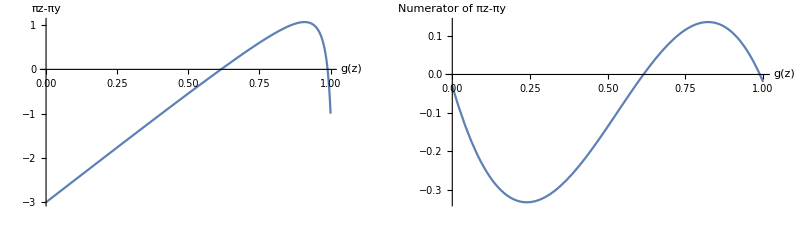

```mathematica
(* Plot f and the cubic numerator of f for r = 3 and e = e1 = 0.01 *)
GraphicsRow[{Plot[Evaluate[r*(2*g-Qdg*g-1)-g//.{r->3,ϵ->(1-0.01)^2+0.01^2,e-> 0.01}],{g,0,1},AxesLabel->{"g(z)","πz-πy"}],
Plot[Evaluate[polyzy//.{r->3,ϵ->(1-0.01)^2+0.01^2,e-> 0.01}],{g,0,1},AxesLabel->{"g(z)","Numerator of πz-πy"}]}]
```

```mathematica
(* Find the cubic numerator of f = πz - πx (given a postive denominator). *)
numdomzx=NumeratorDenominator[Together[r*(2*g-Qcg*g-1)+1-g]];
polyzx = Assuming[r>1&&1>ϵ>0.5>e>0&&1>g>0,FullSimplify@Sign[numdomzx[[2]]]]*numdomzx[[1]];
{a0,a1,a2,a3}=Simplify[CoefficientList[polyzx,g]];
```

```mathematica
(* The cubic's coefficients. *)
Assuming[r>1&&1>ϵ>0.5>e>0,FullSimplify@Reduce[a0<0]]
Assuming[r>1&&1>ϵ>0.5>e>0,FullSimplify@Reduce[¬(a1<0&&a3>0)]]
Assuming[r>1&&1>ϵ>0.5>e>0,FullSimplify@Reduce[¬(a2>0&&a3>0)]]
Assuming[r>1&&1>ϵ>0.5>e>0,FullSimplify@Reduce[¬(a1>0&&a2>0&&a3>0)]]
Assuming[r>1&&1>ϵ>0.5>e>0,FullSimplify@Reduce[(a1>0&&a2<0&&a3>0)]]
```

True

True

True

«1 more identical outputs»

(2 e r+ϵ>e+r&&(4 e^2+ϵ≥e (3+2 ϵ)||√5+10 e>5))||(e+r<2 e r+ϵ&&4 e^2+ϵ<e (3+2 ϵ))||(ϵ≥Root[3 e^2-6 e^3+3 e^4+(-3 e+4 e^2) #1+(1+e-4 e^2) #1^2+(-1+2 e) #1^3&,1]&&(e (-3+4 e-2 ϵ)+ϵ) (e (2-3 r+e (-3+4 r))-(-1+2 e) (-1+r) ϵ)<0)

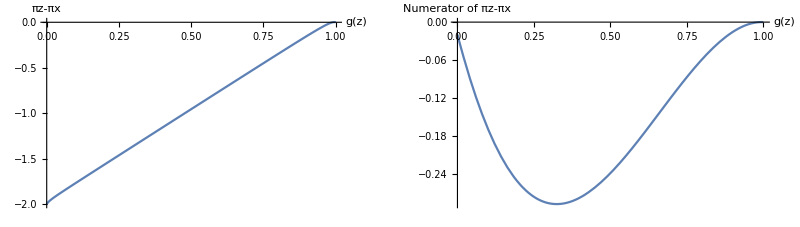

```mathematica
(* Plot f and the cubic numerator of f for r = 3 and e = e1 = 0.01 *)
GraphicsRow[{Plot[Evaluate[r*(2*g-Qcg*g-1)+1-g//.{r->3,ϵ->(1-0.01)^2+0.01^2,e-> 0.01}],{g,0,1},AxesLabel->{"g(z)","πz-πx"}],
Plot[Evaluate[polyzx//.{r->3,ϵ->(1-0.01)^2+0.01^2,e-> 0.01}],{g,0,1},AxesLabel->{"g(z)","Numerator of πz-πx"}]}]
```

```mathematica
(* Show that df/dz = -dg/dz and df/dg = -1 at z=0,1 and g=1. *)
Simplify[D[r*(2*g-1-Qcg*g)+1-g/.{g->g[z]},z]/.{g[z]->1}]
Simplify[D[r*(2*g-1-Qcg*g)+1-g,g]/.{g->1}]
```

-g'[z]

-1

```mathematica
(* Prove that pix=piz on the y-axis. *)
eq1=Collect[Simplify[(1-z)*gx+z*gz-g/.{gx->Qcg*g+1-g,gz->Qcg*g2+Qdg(g-g2)+1-g}],g2];
eq2=Collect[Simplify[z(1-z)*gx^2+(g-(1-z)*gx)^2-z*g2/.{gx->Qcg*g+1-g}],g2];
h=eq1/.{g2*z->eq2+z*g2}
{k0,k1}=Factor[CoefficientList[D[h/.{g->g[z]},z],g'[z]]/.{g[z]->g}];
```

1+g (-2+Qcg-Qcg z+Qdg z)+(Qcg-Qdg) ((g+(1+g (-1+Qcg)) (-1+z))^2-(1+g (-1+Qcg))^2 (-1+z) z)

```mathematica
Assuming[r>1&&1>ϵ>0.5>e>0&&1≥g>0&&g*(2-Qcg)≥ 1&&1≥ Qcg≥ Qdg≥0&&h==0&&1≥z≥0,FullSimplify@Reduce[k0==0]]
Assuming[r>1&&1>ϵ>0.5>e>0&&1≥g>0&&g*(2-Qcg)≥ 1&&1>Qcg>Qdg>0&&h==0&&1≥z≥0,FullSimplify@Reduce[k1<0]]
```

3 g+2 Qcg==5||(Qcg≠1&&(g==2/(3-2 Qcg+√(-3+4 Qcg))||g==-2/(-3+2 Qcg+√(-3+4 Qcg))))||Qcg==Qdg

True